## Fluctuation dissipation relation as equilibrium condition (detailed balance) for FP

```mathematica
gb = E^(-u[x]/T);
(* langevin: dx = - mu D[u[x],x] + Sqrt[2 a] dW;  FP stazionaria associata : *)
fpeq = 0==a D[p[x],{x,2}]+ mu D[p[x]D[u[x],x],x]
Simplify[fpeq/.{p[x]->gb,p'[x]->D[gb,x],p''[x]->D[gb,{x,2}]}] (* nota come si può raccogliere il fattore (a-mu T) *)
Solve[fpeq/.{p[x]->gb,p'[x]->D[gb,x],p''[x]->D[gb,{x,2}]},a]
```

0==a p''[x]+mu (p'[x] u'[x]+p[x] u''[x])

(ⅇ^(-u[x]/T) (a-mu T) (-u'[x]^2+T u''[x]))/T^2==0

{{a→mu T}}

## Generazione dati

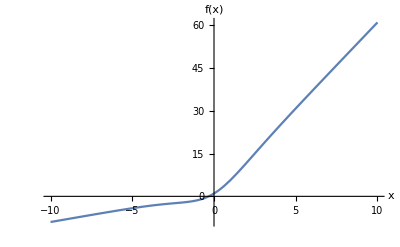

```mathematica
(* setup *)
ftrue[x_]:=1+x(1+5(1+E^(-x))^(-1)); (* modello "vero" dal quale si generano i dati *)
atrue=1; (* In realtà qualunque a > 0 si comporta nello stesso modo; questo è un po' il "problema" di questa funzione obiettivo, ma anche la feature che crea dei minimi con una grande differenza di curvature lungo b; ovviamente è stata scelta in maniera artificiale perché avesse sia minimi molto piccati che minimi molto piatti *)
btrue=5;
fmod[x_,a_,b_]:=x(1+b(1+E^(-a x))^(-1))+a^2; (* NOTA: puoi provare ad aggiungere questo termine a^2 come "penalità" per eliminare gli infiniti minimi con a>0 *)
losssingle[x_,y_,a_,b_]:=(y -fmod[x,a,b])^2; (* questa è solo la parte quadratica, senza somma o normalizzazione*)
gradloss[x_,y_,a_,b_]:={D[(y -fmod[x,a,b])^2,a],D[(y -fmod[x,a,b])^2,b]} ;
Plot[ftrue[x],{x,-10,10},AxesLabel->{"x","f(x)"}]
```

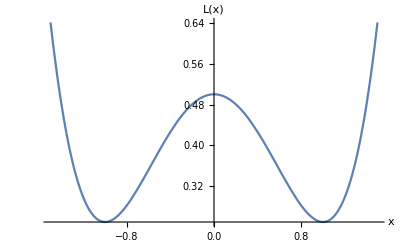

```mathematica
fex[x_]:=1/4x^4-1/2x^2+1/2
Plot[fex[x],{x,-1.5,1.5},AxesLabel->{"x","L(x)"}]
```

```mathematica
(* generate a sample from ftrue*)
nn=30;
ll=20;
ntot=nn ll; (*number of datapoints*)
xs = Table[xi-Floor[nn/2],{ xi,1,nn}];
fi=Table[N[ftrue[x/.(x->xs[[i]])]],{i,1,Length[xs]}];
eps=3;
epss = RandomReal[{-eps,eps},ll*Length[fi]];
data=Table[{xs[[i]],Table[fi[[i]]+epss[[i+j]],{j,0,ll-1}]},{i,1,Length[fi]}];

(******genero dati per l'errore di generalizzazione************)
nnp= Floor[N[nn/5]];
llp = Floor[N[ll/5]];
ntotp=nnp llp; (*number of datapoints*)
xsp = Table[xi-Floor[nnp/2],{ xi,1,nnp}];
fip=Table[N[ftrue[x/.(x->xsp[[i]])]],{i,1,Length[xsp]}];
epssp = RandomReal[{-eps,eps},llp*Length[fip]];
datap=Table[{xsp[[i]],Table[fip[[i]]+epssp[[i+j]],{j,0,llp-1}]},{i,1,Length[fip]}];
lossp[a_,b_]:=(1/ntotp)*Sum[ Sum[(datap[[i,2]][[j]]-fmod[datap[[i,1]],a,b])^2,{j,1,llp}],{i,1,nnp}];(*loss function per il validation set*)
(************************************************************)
```

```mathematica
datawee=Import[FileNameJoin[{$HomeDirectory,"Desktop","tst.mx"}]];
```

## Visualizzo il minimo positivo per vedere se è buono

```mathematica
(*calcolo la loss function su tutto il set di dati, in funzione dei parametri*)
g=Graphics[{PointSize[Large],Blue,Point[{areal,breal}]}];
loss[a_,b_]:=(1/ntot)* Sum[ Sum[(data[[i,2]][[j]]-fmod[data[[i,1]],a,b])^2,{j,1,ll}],{i,1,nn}];

(*Trovo ilm minimo reale della funzione: DEBUG: non è il vero minimo, se confronti la loss function calcolata sul valore vero usato nella generazione dei dati si vede abbastanza chiaramente; i vincoli su x e y come li hai scelti? *)
areal=x/.Last[ FindMinimum[{loss[x,y],Abs[x]<=1.5atrue &&Abs[y]<=1btrue},{x,y}]] 

breal=y/.Last[ FindMinimum[{loss[x,y],Abs[x]<=1.5 atrue &&Abs[y]<=1btrue},{x,y}]]
```

1.04048

5.

a (n opt): 0.969394 b (n opt): 5.

$Aborted

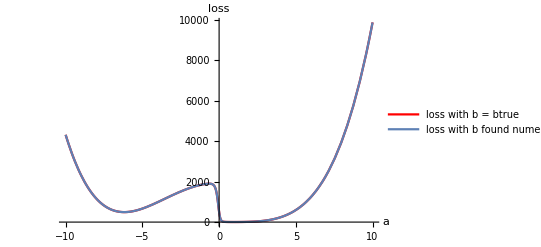

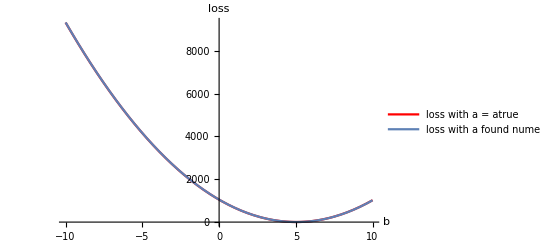

```mathematica
Print["a (n opt): ",areal," b (n opt): ",breal]
l=10;
Plot3D[loss[a,b],{a,-l,l},{b,-l,l}, AxesLabel->{"a","b","loss(a,b)"},PlotRange->All]
Show[
Plot[loss[a,btrue],{a,-l,l}, AxesLabel->{"a","loss"},PlotRange->All,PlotLegends->{"loss with b = btrue"},PlotStyle->Red],
Plot[loss[a,breal],{a,-l,l}, AxesLabel->{"a","loss"},PlotRange->All,PlotLegends->{"loss with b found numerically"}]
]

Show[
Plot[loss[atrue,b],{b,-l,l}, AxesLabel->{"b","loss"},PlotRange->All,PlotLegends->{"loss with a = atrue"},PlotStyle->Red],
Plot[loss[areal,b],{b,-l,l}, AxesLabel->{"b","loss"},PlotRange->All,PlotLegends->{"loss with a found numerically"}]
]
```

## Cerco il minimo negativo per verificare il crossing

```mathematica
(*Trovo il minimo negativo della funzione*)
arealmin=x/.Last[ FindMinimum[{loss[x,y],x<0 },{x,y}]];
brealmin=y/.Last[ FindMinimum[{loss[x,y],x<0 },{x,y}]];
```

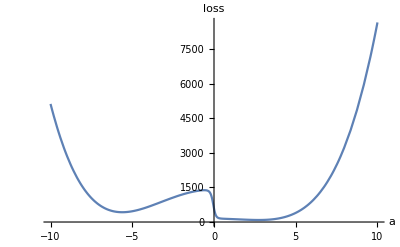

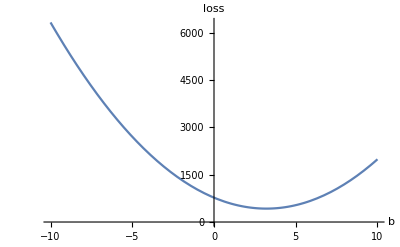

arealmin, brealmin: -5.61068 3.20352

```mathematica
Plot[loss[a,brealmin],{a,-l,l}, AxesLabel->{"a","loss"}]
Plot[loss[arealmin,b],{b,-l,l}, AxesLabel->{"b","loss"}]
Print["arealmin, brealmin: ", arealmin," ",brealmin]
```

## Verifico la formula per il diffusion coeff

```mathematica
(*loss function sul singolo dato*)
losssingle[x_,y_,a_,b_]:=(y -fmod[x,a,b])^2;
bsize=1;
(*matrice hessiana per la loss function*)
hessloss[x_,y_,a_,b_]:= {{D[D[(y -fmod[x,a,b])^2,a],a],D[D[(y -fmod[x,a,b])^2,a],b]},{D[D[(y -fmod[x,a,b])^2,b],a],D[D[(y -fmod[x,a,b])^2,b],b]}};
(*gradiente della loss function*)
gradloss[x_,y_,a_,b_]:={D[(y -fmod[x,a,b])^2,a],D[(y -fmod[x,a,b])^2,b]};

gradlosstot[a_,b_]:=(1/ntot)*Sum[Sum[gradloss[data[[i,1]],data[[i,2]][[j]],x,y],{j,1,ll}],{i,1,nn}]/.{x->a,y->b};

covariance[a_,b_]:=(1/(bsize*ntot))*(Sum[Sum[Outer[Times,gradloss[data[[i,1]],data[[i,2]][[j]],x,y],gradloss[data[[i,1]],data[[i,2]][[j]],x,y]],{j,1,ll}],{i,1,nn}]-ntot*Outer[Times,gradlosstot[x,y],gradlosstot[x,y]]/.{x->a,y->b});

(*hessiana valutata nel minimo*)
hesslossmin= Sum[Sum[hessloss[data[[i,1]],data[[i,2]][[j]],x,y]/.{x->areal,y->breal},{j,1,ll}],{i,1,nn}];
(*differenza tra l'approssimazione del paper e il calcolo esatto*)
difference[a_,b_]:=covariance[x,y]-(2*loss[x,y]/bsize)*hesslossmin/.{x->a,y->b};
normeddiff[a_,b_]:=Abs[Norm[difference[x,y],"Frobenius"]]/.{x->a,y->b};
(*Plot3D[normeddiff[a,b],{a,-2,3},{b,-3,6}, AxesLabel->{"a","b","loss(a,b)"},PlotRange->All]*)
(*relativeerr[a_,b_]:=Abs[Norm[difference[x,y],"Frobenius"]/Norm[covariance[x,y],"Frobenius"]]/.{x->a,y->b};*)
```

```mathematica
normeddiff[areal,breal]
```

305382.

```mathematica
normeddiff[areal,breal]
```

273392.

```mathematica
loss[areal,breal]
loss[atrue,btrue]
loss[arealmin,brealmin]
loss[asaddleprecise,bsaddleprecise]
```

2.62572

2.70503

424.579

1059.47

```mathematica
normeddiff[arealmin, brealmin]
normeddiff[asaddleprecise,bsaddleprecise]
```

1.9366×10^8

4.8276×10^8

```mathematica
Eigenvalues[difference[areal, breal]]
difference[asaddleprecise,bsaddleprecise]
```

{-271243.,-34209.}

{{-1.87489×10^7,-2.11555×10^7},{-2.11555×10^7,-1.04708×10^8}}

```mathematica
s=20;
(*costruisco una griglia di punti su cui valutare la funzione*)
xgrid=Subdivide[0.5,1.5,s];
ygrid= Subdivide[4.5,5.5,s];
grid = Outer[List,xgrid,ygrid];
vectorgrid= ArrayReshape[grid, {(s+1)^2,2}];
sampling=Table[normeddiff[vectorgrid[[i]][[1]],vectorgrid[[i]][[2]]],{i,1,(s+1)^2}];
samplingscatter=Table[{vectorgrid[[i]][[1]],vectorgrid[[i]][[2]],sampling[[i]]},{i,1,(s+1)^2}];
(*ListDensityPlot[samplingscatter,AxesLabel->{"a","b"}]*)
```

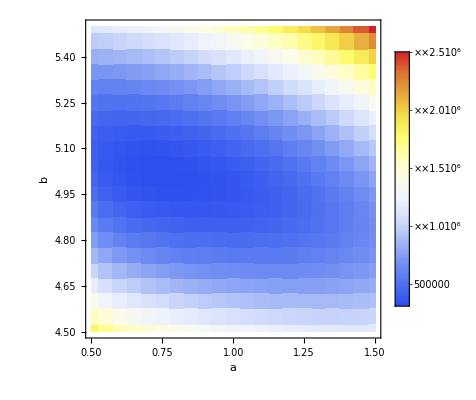

```mathematica
ListDensityPlot[samplingscatter,InterpolationOrder->0,ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"a","b"}]
```

## Genero il punto di partenza

```mathematica
a0 =RandomReal[];(*{0.75,1.25}*)
b0=RandomReal[];(*{4.75,5.25}*)
(*a0 =-5;
b0=3;*)
Print["a0, b0: ", a0," ",b0]
```

a0, b0: 0.692821 0.245602

## Sampling dello SGD

```mathematica
numeta=Table[i,{i,4,4}];
numpath=1;
bsize =2;
```

```mathematica
(*questo codice analizza le proprietà statistiche di realizzazioni con lo stesso starting point, ma sotto ho un codice che simula cammini con diversi starting point e uno che studia solo il punto di convergenza che è molto più efficiente, quindi non è un problema cambiarlo*)
maxite =40000;
v= Table[Table[Table[{0,0},{ite,1,maxite}],{j,1,numpath}],{k,1,Length[numeta]}];
(*Per ogni eta simulo numpath cammini con maxite iterazioni *)
For[k=1, k≤ Length[numeta],k++,

(* IPERPARAMETRI DEL SGD *)

eta =10^(-numeta[[k]]);
For[j=1, j ≤ numpath,j++, 
(* costruisco il vettore dei parametri che ottimizzo, tengo tutti le iterazioni per la visualizzazione *)
lossvalues=Table[0,{ite,1,maxite}]; (* per visualizzazione *)
totlossvalues=Table[0,{ite,1,maxite}]; (* sarebbe la loss usata nel GD *)
v[[k]][[j]][[1]]={a0,b0};
(* SGD loop **************************************************************)
(* nota: faccio il caso semplice del ciclo for, si può sostituire con un while per controllare se sta raggiungendo la convergenza *)
For[ite=2,ite<=maxite, ite++,
If[Mod[ite,10000]==0, Print["ite: ",ite, "/ ", maxite]];
ai = v[[k]][[j]][[ite-1]][[1]];
bi= v[[k]][[j]][[ite-1]][[2]];

(* sceglie il nuovo minibatch *)
xidxs =RandomInteger[{1,nn},bsize];
yidxs=RandomInteger[{1,ll},bsize]; (* nota che si fa così solo per il modo in cui ho costruito i dati, in generale non devi scegliere x e y in maniera indipendente!*)
xis =Table[ data[[xidxs[[bidx]],1]], {bidx,1,bsize}];
yis = Table[data[[xidxs[[bidx]],2]][[yidxs[[bidx]] ]],{bidx,1,bsize}];


(* solo per visualizzazione; calcolo la loss function per il minibatch *)  
lossvalues[[ite]]= 1/bsize 
 Sum[
N[loss[xis[[bidx]],yis[[bidx]], ai,bi]],
{bidx,1,bsize}
];

(* calcola il gradiente medio della loss rispetto ai parametri *) 
gradlossvector= 1/bsize 
 Sum[
(gradloss[xis[[bidx]],yis[[bidx]], z1,z2]/.{z1->ai,z2->bi}),
{bidx,1,bsize}
];

(* calcola l'incremento *)
dai =eta gradlossvector[[1]];
dbi =eta gradlossvector[[2]];
v[[k]][[j]][[ite]]={ai-dai, bi-dbi};
If[Mod[ite,10000]==0, Print[v[[k]][[j]][[ite]]]];
]]]
```

```mathematica
Export[FileNameJoin[{$HomeDirectory,"Desktop","vsamestarting.mx"}],v];
```

## Sampling dello SGD, cambio starting point

```mathematica
numeta=Table[i,{i,5,5}];
numpath=1;
bsize =1;
```

```mathematica
randomstart=Table[{RandomReal[{0,2}],RandomReal[{3,7}]},{i,1,numpath}]
```

```mathematica
randomstart
```

{{1.29475,5.12551},{1.54332,5.01656},{1.62873,5.76949},{1.42712,3.05737},{0.834672,5.98081},{1.49567,6.63389}}

```mathematica
(*questo codice analizza le proprietà statistiche di realizzazioni con lo stesso starting point, ma sotto ho un codice che simula cammini con diversi starting point e uno che studia solo il punto di convergenza che è molto più efficiente, quindi non è un problema cambiarlo*)

maxite =120000;
(*v= Table[Table[{0,0},{j,1,numpath}],{k,1,Length[numeta]}];*)
v={0,0};
vitecount={0};
(*Per ogni eta simulo numpath cammini con maxite iterazioni *)
For[k=1, k≤ Length[numeta],k++,
Print["numeta: ",k];
(* IPERPARAMETRI DEL SGD *)

eta =10^(-numeta[[k]]);
For[j=1, j ≤ numpath,j++, 
Print["numpath: ",j];
vcurrent={2,2};
vprev=vcurrent;
ite=2;
While[Abs[areal-vcurrent[[1]]]≥ 0.05 ||Abs[breal-vcurrent[[2]]]≥ 0.05 &&ite≤120000,
If[Mod[ite,10000]==0, Print["ite: ",ite]];
vprev = vcurrent;

(* sceglie il nuovo minibatch *)
xidxs =RandomInteger[{1,nn},bsize];
yidxs=RandomInteger[{1,ll},bsize]; (* nota che si fa così solo per il modo in cui ho costruito i dati, in generale non devi scegliere x e y in maniera indipendente!*)
xis =Table[ data[[xidxs[[bidx]],1]], {bidx,1,bsize}];
yis = Table[data[[xidxs[[bidx]],2]][[yidxs[[bidx]] ]],{bidx,1,bsize}];

(* calcola il gradiente medio della loss rispetto ai parametri *) 
gradlossvector= 1/bsize 
 Sum[
(gradloss[xis[[bidx]],yis[[bidx]], z1,z2]/.{z1->vprev[[1]],z2->vprev[[2]]}),
{bidx,1,bsize}
];

(* calcola l'incremento *)
ai =eta gradlossvector[[1]];
bi =eta gradlossvector[[2]];
vcurrent[[1]]=vprev[[1]]-ai;
vcurrent[[2]]=vprev[[2]]-bi;
If[Mod[ite,10000]==0, Print[vcurrent]];
ite++;
(*v[[k]][[j]][[1]]=vprev[[1]];
v[[k]][[j]][[2]]=vprev[[2]];*)
v=Append[v,vcurrent];
];
vitecount=Append[vitecount,ite];
];
]
```

numeta: 1

numpath: 1

ite: 10000

{1.47871,4.8847}

ite: 20000

{1.12572,4.99365}

```mathematica
vitecount
```

{0,1097,1744,1473,2164,3224,469}

numpath: 6

```mathematica
arealmin
brealmin
```

-5.6281

3.20277

```mathematica
v[[1097+1742+1471+2162+3222+467]]
```

{0.99577,5.04997}

```mathematica
v
```

{0,0,{2.00188,2.00422},{2.00406,2.00968},26017,{1.01973,5.02198},{1.01964,5.02198},{1.01949,5.02181},{1.01937,5.02181}}
 |  |  |  |

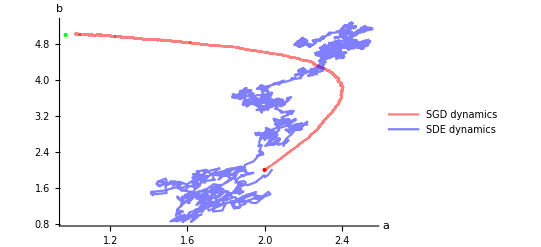

```mathematica
p1=ListLinePlot[Table[{v[[ite]][[1]],v[[ite]][[2]]},{ite,3,Length[v]}],PlotLegends->{"SGD dynamics"},PlotStyle->{Red,Opacity[0.5]},
AxesLabel->{"a","b"},PlotRange->All];
p2=ListLinePlot[Table[{vc[[ite]][[1]],vc[[ite]][[2]]},{ite,2,Length[vc]}],PlotLegends->{"SDE dynamics"},PlotStyle->{Blue,Opacity[0.5]},
AxesLabel->{"a","b"},PlotRange->All];
g=Graphics[{PointSize[Large],Green,Point[{areal,breal}]}];
g1=Graphics[{PointSize[Large],Red,Point[{2,2}]}];
Show[p1,p2,g,g1,PlotRange->All]
```

## Proprietà statistiche della SGD dynamics

```mathematica
astat=Table[{0,0},{q,1,Length[numeta]}];
astatdata= Table[0,{qq,1,numpath}];
bstat=Table[{0,0},{q,1,Length[numeta]}];
bstatdata= Table[0,{qq,1,numpath}];
(*vado a mediare su tutti numpath gli numeta risultati di convergenza, guardo la deviazione standard*)
For[i=1, i ≤ Length[numeta], i++,
For[j=1,j ≤ numpath,j++,
astatdata[[j]]= v[[i]][[j]][[1]];
bstatdata[[j]]= v[[i]][[j]][[2]];
];

astat[[i]]={Mean[astatdata],StandardDeviation[astatdata]};
bstat[[i]]={Mean[bstatdata],StandardDeviation[bstatdata]};
Print[bstat[[i]]];
];

Print[bstat]
```

{4.98091,0.0086428}

{5.05442,0.0443097}

{{4.98091,0.0086428},{5.05442,0.0443097}}

1.32482

## Confronto degli ensamble per SGD

```mathematica
astatpath= Table[Table[{0,0}, {i,1,maxite}],{j,1,Length[numeta]}];
astatpathdata= Table[0,{i,1,numpath}];
bstatpath= Table[Table[{0,0}, {i,1,maxite}],{j,1,Length[numeta]}];
bstatpathdata= Table[0,{i,1,numpath}];
(* Guardo come evolvono mediamente i parametri e la deviazione standard del cammino per i vari eta*)

For[i=1,i ≤ Length[numeta],i++,
For[j=1, j ≤ maxite, j++,
For[k=1, k ≤ numpath,k++,
astatpathdata[[k]] = v[[i]][[k]][[j]][[1]];
bstatpathdata[[k]] = v[[i]][[k]][[j]][[2]];
];
astatpath[[i]][[j]][[1]]=Mean[astatpathdata];
astatpath[[i]][[j]][[2]]=StandardDeviation[astatpathdata];
bstatpath[[i]][[j]][[1]]=Mean[bstatpathdata];
bstatpath[[i]][[j]][[2]]=StandardDeviation[bstatpathdata];
];
];
```

```mathematica
Dimensions[astatpath]
```

{4,40000,2}

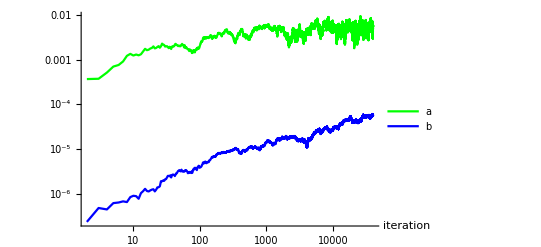

```mathematica
Show[
ListLinePlot[Table[{ite,astatpath[[1]][[ite]][[2]]},{ite,1,maxite}],
AxesOrigin->{0,0},
AxesLabel->{"iteration",""} ,ScalingFunctions->{"Log","Log"},PlotLegends->{"a"},PlotStyle->{Green}],
ListLinePlot[Table[{ite,astatpath[[4]][[ite]][[2]]},{ite,1,maxite}],AxesOrigin->{0,0},ScalingFunctions->{"Log","Log"},
PlotLegends->{"b"},PlotStyle->{Blue}],PlotRange->All
]
```

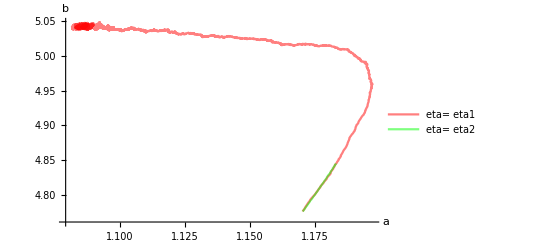

```mathematica
pathsgd1=ListLinePlot[Table[{astatpath[[1]][[ite]][[1]],bstatpath[[1]][[ite]][[1]]},{ite,1,maxite}],PlotLegends->{"eta= eta1"},PlotStyle->{Red,Opacity[0.5]},
AxesLabel->{"a","b"},PlotRange->All];
pathsgd2=ListLinePlot[Table[{astatpath[[4]][[ite]][[1]],bstatpath[[4]][[ite]][[1]]},{ite,1,maxite}],PlotLegends->{"eta= eta2"},PlotStyle->{Green,Opacity[0.5]},
AxesLabel->{"a","b"},PlotRange->All];
Show[pathsgd1,pathsgd2]
```

## Sampling della SDE

```mathematica
timestep=etasgd;
maxtimes=2000;
bsizesgd =bsize;
vc= Table[Table[Table[{0,0},{ite,1,maxtimes}],{j,1,numpath}],{k,1,Length[numeta]}];



(*calcolo l'hessiano, lo valuto su tutto il set e nel punto di minimo nello spazio dei parametri(che conosco)*)
hessloss[x_,y_,a_,b_]:= {{D[D[(y -fmod[x,a,b])^2,a],a],D[D[(y -fmod[x,a,b])^2,a],b]},{D[D[(y -fmod[x,a,b])^2,b],a],D[D[(y -fmod[x,a,b])^2,b],b]}};


(*vauluto l'hessiano nel minimo reale*)
hesslossmin= Sum[Sum[hessloss[data[[i,1]],data[[i,2]][[j]],x,y]/.{x->areal,y->breal},{j,1,ll}],{i,1,nn}];
sqrthesslossmin=MatrixPower[ hesslossmin, 1/2];

(*calcolo il gradiente su tutto il set di dati*)
gradlosstot[a_,b_]:=(1/ntot)*Sum[Sum[gradloss[data[[i,1]],data[[i,2]][[j]],x,y],{j,1,ll}],{i,1,nn}]/.{x->a,y->b}

(*calcolo la dinamica*)
For[k=1, k≤ Length[numeta],k++,
etasgd= 10^(-numeta[[k]]);

For[j=1, j ≤ numpath,j++,
vc[[k]][[j]][[1]]={a0,b0};

For[ite=2,ite≤maxtimes, ite++,
Z={RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]};
Zscale= sqrthesslossmin.Z;
ai = vc[[k]][[j]][[ite-1]][[1]];
bi= vc[[k]][[j]][[ite-1]][[2]];
vc[[k]][[j]][[ite]][[1]]= ai-gradlosstot[x,y][[1]]*timestep+Sqrt[(2*etasgd/bsizesgd)*loss[x,y]]*Zscale[[1]]*Sqrt[timestep]/.{x->ai,y->bi};
vc[[k]][[j]][[ite]][[2]]= bi-gradlosstot[x,y][[2]]*timestep+Sqrt[(2*etasgd/bsizesgd)*loss[x,y]]*Zscale[[2]]*Sqrt[timestep]/.{x->ai,y->bi};
If[Mod[ite,100]==0, Print[ite, ", ", vc[[k]][[j]][[ite]]]];
];
];
]
```

# Sampling SDE variando starting point

```mathematica
numeta=Table[i,{i,5,5}];
numpath=1;
bsize =1;
timestep=etasgd;
maxtimes=2000;
bsizesgd =bsize;
(*vc= Table[Table[{0,0},{j,1,numpath}],{k,1,Length[numeta]}];
*)
```

```mathematica
randomstart=Table[{RandomReal[{0,2}],RandomReal[{3,7}]},{i,1,numpath}]
```

{{1.29475,5.12551},{1.54332,5.01656},{1.62873,5.76949},{1.42712,3.05737},{0.834672,5.98081},{1.49567,6.63389}}

```mathematica
{{1.5452044368265767,6.979008122881188},{1.8794181239230245,3.4023553571674015},{0.690570381217992,5.40948642045809},{1.7435335642137142,3.098056994568961},{0.5018166915082038,4.657410285749719},{0.07039001898062613,4.025743840763232},{0.4157462581058562,4.259748837598978},{1.5673019400733308,5.813812538709655},{0.4060080561642172,6.650919656977757},{0.38827889940924987,5.662469717214666}}
```

```mathematica
Export[FileNameJoin[{$HomeDirectory,"Desktop","randomstart21/03.mx"}],randomstart]
```

C:\Users\jackv\Desktop\randomstart21\03.mx

```mathematica
areal
breal
```

0.969394

5.

```mathematica
(*calcolo l'hessiano, lo valuto su tutto il set e nel punto di minimo nello spazio dei parametri(che conosco)*)
hessloss[x_,y_,a_,b_]:= {{D[D[(y -fmod[x,a,b])^2,a],a],D[D[(y -fmod[x,a,b])^2,a],b]},{D[D[(y -fmod[x,a,b])^2,b],a],D[D[(y -fmod[x,a,b])^2,b],b]}};


(*vauluto l'hessiano nel minimo reale*)
hesslossmin= Sum[Sum[hessloss[data[[i,1]],data[[i,2]][[j]],x,y]/.{x->areal,y->breal},{j,1,ll}],{i,1,nn}];
sqrthesslossmin=MatrixPower[ hesslossmin, 1/2];

(*calcolo il gradiente su tutto il set di dati*)
gradlosstot[a_,b_]:=(1/ntot)*Sum[Sum[gradloss[data[[i,1]],data[[i,2]][[j]],x,y],{j,1,ll}],{i,1,nn}]/.{x->a,y->b}
```

```mathematica
vc={{0,0}};
vcconv={{0,0}};
itecount={0};



(*calcolo la dinamica*)
For[k=1, k≤ Length[numeta],k++,
etasgd= 10^(-numeta[[k]]);
timestep=etasgd;
Print["numeta: ",k];

For[j=1, j ≤ numpath,j++,
vcurrent={2,2};
vprev=vcurrent;
Print["numpath: ",j];
ite=2;
(*loss[vcurrent[[1]],vcurrent[[2]]]≥ 1.01*loss[areal,breal]*)
While[Abs[areal-vcurrent[[1]]]≥ 0.05 ||Abs[breal-vcurrent[[2]]]≥ 0.05,
Z={RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]};
Zscale= sqrthesslossmin.Z;
vprev=vcurrent;
ai = vprev[[1]];
bi=vprev[[2]];
vcurrent[[1]]= ai-gradlosstot[x,y][[1]]*timestep+Sqrt[(2*etasgd/bsizesgd)*loss[x,y]]*Zscale[[1]]*Sqrt[timestep]/.{x->ai,y->bi};
vcurrent[[2]]= bi-gradlosstot[x,y][[2]]*timestep+Sqrt[(2*etasgd/bsizesgd)*loss[x,y]]*Zscale[[2]]*Sqrt[timestep]/.{x->ai,y->bi};
If[Mod[ite,100]==0, Print[ite, ", ", vcurrent]];
ite++;
vc=Append[vc,{vcurrent[[1]],vcurrent[[2]]}];
];
itecount=Append[itecount,ite];
vcconv=Append[vc,{vcurrent[[1]],vcurrent[[2]]}];
];
]
```

numeta: 1

numpath: 1

100, {1.54541,0.855507}

200, {1.69564,1.34411}

300, {1.41274,1.51228}

400, {1.79434,1.8738}

500, {1.98934,2.71742}

600, {2.13854,3.08402}

700, {2.12769,3.25497}

800, {1.98686,3.38685}

900, {1.99223,3.41316}

1000, {1.92591,3.68935}

1100, {1.875,3.68699}

1200, {2.00421,3.53356}

1300, {1.99801,3.74989}

1400, {2.19897,4.25386}

1500, {2.24144,4.24193}

1600, {2.27239,4.27306}

1700, {2.30557,4.45163}

1800, {2.34788,4.5543}

1900, {2.33647,4.6674}

2000, {2.31193,4.64331}

2100, {2.34306,4.5229}

2200, {2.42239,4.6069}

2300, {2.45344,4.81753}

2400, {2.3957,4.7417}

2500, {2.36924,4.76514}

2600, {2.34428,4.70094}

2700, {2.38585,4.87099}

2800, {2.4803,4.74082}

2900, {2.53823,4.89468}

3000, {2.44919,4.85418}

3100, {2.4503,4.99458}

3200, {2.41884,5.07621}

3300, {2.39723,5.08748}

3400, {2.29607,4.91309}

3500, {2.18019,4.76281}

3600, {2.19677,4.82113}

3700, {2.18871,4.91366}

$Aborted

```mathematica
vc
```

{{0,0},{2.04054,2.01521},{2.01668,1.88192},3716,{2.18493,4.87893},{2.18696,4.86872},{2.18627,4.88057}}
 |  |  |  |

```mathematica
itecount
```

{0,218,373,1542,2451,1818,441}

numpath: 6

```mathematica
itecount=itecount[[3;;Length[itecount]]]
```

{480,845,843,1873,1591,942}

```mathematica
vc[[372+216+1540+2449+1816+439]]
```

{0.998746,5.03586}

```mathematica
areal
breal
```

0.969394

5.

```mathematica
Export[FileNameJoin[{$HomeDirectory,"Desktop","continuouspath21/03.mx"}],vc]
```

C:\Users\jackv\Desktop\continuouspath21\03.mx

```mathematica
p1=ListLinePlot[Table[{vc[[ite]][[1]],vc[[ite]][[2]]},{ite,2,217}],PlotLegends->{"SGD dynamics, ensemble 1"},PlotStyle->{Red,Opacity[0.5]},
AxesLabel->{"a","b"},PlotRange->All];
p2=ListLinePlot[Table[{vc[[ite]][[1]],vc[[ite]][[2]]},{ite,218,372+216}],PlotLegends->{"SGD dynamics,ensemble 2"},PlotStyle->{Blue,Opacity[0.5]},
AxesLabel->{"a","b"},PlotRange->All];
g=Graphics[{PointSize[Large],Green,Point[{areal,breal}]}];
g1=Graphics[{PointSize[Large],Red,Point[{randomstart[[1]][[1]],randomstart[[1]][[2]]}]}];
g2=Graphics[{PointSize[Large],Blue,Point[{randomstart[[2]][[1]],randomstart[[2]][[2]]}]}];
Show[p1,p2,g,g1,g2,PlotRange->All]
```

```mathematica
vc
```

{{0,0},{1.29981,5.15011},{1.30608,5.15224},4929,{1.00122,5.07216},{1.00294,5.06726},{1.02045,5.05266}}
 |  |  |  |

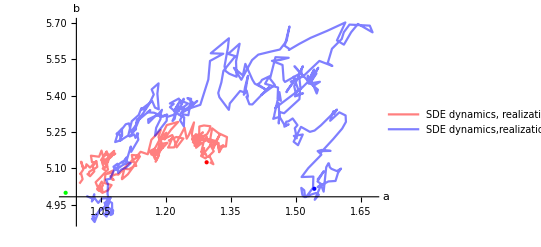

```mathematica
p1=ListLinePlot[Table[{vc[[ite]][[1]],vc[[ite]][[2]]},{ite,2,217}],PlotLegends->{"SDE dynamics, realization 1"},PlotStyle->{Red,Opacity[0.5]},
AxesLabel->{"a","b"},PlotRange->All];
p2=ListLinePlot[Table[{vc[[ite]][[1]],vc[[ite]][[2]]},{ite,218,372+216}],PlotLegends->{"SDE dynamics,realization 2"},PlotStyle->{Blue,Opacity[0.5]},
AxesLabel->{"a","b"},PlotRange->All];
g=Graphics[{PointSize[Large],Green,Point[{areal,breal}]}];
g1=Graphics[{PointSize[Large],Red,Point[{randomstart[[1]][[1]],randomstart[[1]][[2]]}]}];
g2=Graphics[{PointSize[Large],Blue,Point[{randomstart[[2]][[1]],randomstart[[2]][[2]]}]}];
Show[p1,p2,g,g1,g2,PlotRange->All]
```

```mathematica
areal
```

0.969394

## Proprietà statistiche della SDE

```mathematica
vcastat=Table[{0,0},{q,1,Length[numeta]}];
vcastatdata= Table[0,{qq,1,numpath}];
vcbstat=Table[{0,0},{q,1,Length[numeta]}];
vcbstatdata= Table[0,{qq,1,numpath}];

For[i=1, i ≤ Length[numeta], i++,
For[j=1,j ≤ numpath,j++,
vcastatdata[[j]]= vc[[i]][[j]][[-1]][[1]];
vcbstatdata[[j]]= vc[[i]][[j]][[-1]][[2]];
];

vcastat[[i]]={Mean[vcastatdata],StandardDeviation[vcastatdata]};
vcbstat[[i]]={Mean[vcastatdata],StandardDeviation[vcbstatdata]}
];
```

StandardDeviation::shlen: The argument {0.944059} should have at least two elements.

StandardDeviation::shlen: The argument {4.22533} should have at least two elements.

## Confronto degli ensamble per SDE

```mathematica
vcastatpath= Table[Table[{0,0}, {i,1,maxtimes}],{j,1,Length[numeta]}];
vcastatpathdata= Table[0,{i,1,numpath}];
vcbstatpath= Table[Table[{0,0}, {i,1,maxtimes}],{j,1,Length[numeta]}];
vcbstatpathdata= Table[0,{i,1,numpath}];
For[i=1,i ≤ Length[numeta],i++,
For[j=1, j ≤ maxtimes, j++,
For[k=1, k ≤ numpath,k++,
vcastatpathdata[[k]] = vc[[i]][[k]][[j]][[1]];
vcbstatpathdata[[k]] = vc[[i]][[k]][[j]][[2]];
];
vcastatpath[[i]][[j]][[1]]=Mean[vcastatpathdata];
vcastatpath[[i]][[j]][[2]]=StandardDeviation[vcastatpathdata];
vcbstatpath[[i]][[j]][[1]]=Mean[vcbstatpathdata];
vcbstatpath[[i]][[j]][[2]]=StandardDeviation[vcbstatpathdata];
];
];
```

StandardDeviation::shlen: The argument {0.753931} should have at least two elements.

StandardDeviation::shlen: The argument {4.88143} should have at least two elements.

StandardDeviation::shlen: The argument {0.743278} should have at least two elements.

General::stop: Further output of StandardDeviation::shlen will be suppressed during this calculation.

## Training tramite GD

```mathematica
maxite2=1002;
eta = etasgd;
vgd = Table[{0,0},{ite,1,maxite2}];
vgd[[1]]={a0,b0};
For[ite=2,ite<=maxite2, ite++,
ai = vgd[[ite-1]][[1]];
bi= vgd[[ite-1]][[2]];

(* calcola l'incremento *)
dai =eta gradlosstot[x,y][[1]]/.{x->ai,y->bi};
dbi =eta gradlosstot[x,y][[2]]/.{x->ai,y->bi};
vgd[[ite]]={ai-dai, bi-dbi};
If[Mod[ite,100]==0, Print[ite, ", ", vgd[[ite]]]];
]
```

100, {0.767293,2.84734}

200, {1.01362,4.05155}

300, {1.12278,4.55953}

400, {1.1633,4.773}

500, {1.17341,4.86342}

600, {1.17117,4.90261}

700, {1.16437,4.92041}

800, {1.15622,4.9292}

900, {1.148,4.93412}

1000, {1.1402,4.93732}

## Verifica dell’escape rate

### Stimo il punto di sella numericamente

```mathematica
(*campiono i minimi nella zona attorno al punto di sella*)
numpoints=5;
parts= Subdivide[2,6,numpoints];
sad=Table[{0,0},{ite,1,numpoints}];

For[i=1, i≤numpoints,i++,
areal=x/.Last[ FindMinimum[{loss[x,parts[[i]]],x>0},{x}]];
arealmin=x/.Last[ FindMinimum[{loss[x,parts[[i]]],x<0},{x}]];
sad[[i]]={x/.Last[ FindMaximum[{loss[x,parts[[i]]],arealmin<x<areal},{x}]],parts[[i]]};
Print[sad[[i]]];
];
```

{-0.537054,2}

{-0.576465,14/5}

{-0.607413,18/5}

{-0.633115,22/5}

{-0.655216,26/5}

```mathematica
dummymax=Table[0,{ite,1,numpoints}];
dummya= Table[0,{ite,1,numpoints}];
For[i=1, i≤numpoints,i++,
dummymax[[i]]=loss[sad[[i]][[1]],parts[[i]]];
dummya[[i]]=sad[[i]][[1]];
];
     maxa=Max[dummymax];
positiona=Position[dummymax,maxa][[1,1]];
saddlereal={dummya[[positiona]],parts[[positiona]]};
Print[saddlereal];
```

{-0.652809,26/5}

#### secondo approccio

```mathematica
(*cerco i punti in cui il gradiente si annulla*)
gradlosstot[a_,b_]:=(1/ntot)*Sum[Sum[gradloss[data[[i,1]],data[[i,2]][[j]],x,y],{j,1,ll}],{i,1,nn}]/.{x->a,y->b};
asaddleprecise=x/.FindRoot[{gradlosstot[x,y][[1]],gradlosstot[x,y][[2]]},{{x,-0.6},{y,25/6}}];
bsaddleprecise=y/.FindRoot[{gradlosstot[x,y][[1]],gradlosstot[x,y][[2]]},{{x,-0.6},{y,25/6}}];

hessloss[x_,y_,a_,b_]:= {{D[D[(y -fmod[x,a,b])^2,a],a],D[D[(y -fmod[x,a,b])^2,a],b]},{D[D[(y -fmod[x,a,b])^2,b],a],D[D[(y -fmod[x,a,b])^2,b],b]}};

hesslosssaddle= Sum[Sum[hessloss[data[[i,1]],data[[i,2]][[j]],x,y]/.{x->asaddleprecise,y->bsaddleprecise},{j,1,ll}],{i,1,nn}];
Print[Eigenvalues[hesslosssaddle]];
```

{-219177.,62195.8}

```mathematica
loss[asaddleprecise,bsaddleprecise]
```

1059.47

```mathematica
normeddiff[asaddleprecise,bsaddleprecise]
```

1.10501×10^8

### Stima teorica per l’escape rate

```mathematica
(*calcolo l'escape con la formula di [Mori] in funzione dei parametri*)
hesslossmin= Sum[Sum[hessloss[data[[i,1]],data[[i,2]][[j]],x,y]/.{x->areal,y->breal},{j,1,ll}],{i,1,nn}];
hminmax=Max[Eigenvalues[hesslossmin]];
hsaddlemin=Min[Eigenvalues[hesslosssaddle]];
(*escapemori[eta_,bsize_]:=(Sqrt[hminmax*hsaddlemax]/2*Pi)(loss[x,y]/loss[z,q])^(-bsize/(eta*hminmax)){x->asaddleprecise,y->bsaddleprecise,z->areal,q->breal};
*)
```

```mathematica
escapemori[eta_,bsize_]:=(Sqrt[hminmax*Abs[hsaddlemin]]/2*Pi)*(loss[asaddleprecise,bsaddleprecise]/loss[areal,breal])^(-bsize/(eta*hminmax));


escapekramer[diff_]:=(Sqrt[hminmax*hsaddlemax]/2*Pi)*Exp[-diff*(loss[asaddleprecise,bsaddleprecise]-loss[areal,breal])]
Print[1/escapemori[0.0023,1]];
Print[escapekramer[0.00001]];
```

6.22371×10^-6

166687.

```mathematica
arealmin
```

-5.67178

```mathematica
loss[asaddleprecise,bsaddleprecise]/loss[areal,breal]
```

```mathematica
352.42566655106486
```

```mathematica
hminmax
```

51767.5

### Escape time per SGD

```mathematica
(* IPERPARAMETRI DEL SGD *)
maxite =30000;
eta =0.0023;
bsize =1;

(* costruisco il vettore dei parametri che ottimizzo, tengo tutti le iterazioni per la visualizzazione *)
lossvalues=Table[0,{ite,1,maxite}]; (* per visualizzazione *)
totlossvalues=Table[0,{ite,1,maxite}]; (* sarebbe la loss usata nel GD *)
v={{arealmin,brealmin}};
vprev={arealmin,brealmin};
vcurrent = {arealmin,brealmin};
(* SGD loop **************************************************************)


ite=2;
While[vcurrent[[1]]<0.5||vcurrent[[2]]<4.5,
If[Mod[ite,10000]==0, Print["ite: ",ite]];
vprev=vcurrent;
ai=vprev[[1]];
bi=vprev[[2]];
(* sceglie il nuovo minibatch *)
xidxs =RandomInteger[{1,nn},bsize];
yidxs=RandomInteger[{1,ll},bsize]; (* nota che si fa così solo per il modo in cui ho costruito i dati, in generale non devi scegliere x e y in maniera indipendente!*)
xis =Table[ data[[xidxs[[bidx]],1]], {bidx,1,bsize}];
yis = Table[data[[xidxs[[bidx]],2]][[yidxs[[bidx]] ]],{bidx,1,bsize}];

(* calcola il gradiente medio della loss rispetto ai parametri *) 
gradlossvector= 1/bsize 
 Sum[
(gradloss[xis[[bidx]],yis[[bidx]], z1,z2]/.{z1->ai,z2->bi}),
{bidx,1,bsize}
];

(* calcola l'incremento *)
vcurrent[[1]] =ai-eta gradlossvector[[1]];
vcurrent[[2]] =bi-eta gradlossvector[[2]];
If[Mod[ite,10000]==0, Print[vcurrent](*&& v=Append[v,{vcurrent[[1]],vcurrent[[2]]}]*)];
ite++;
];Print[vcurrent]
Print["ite: ",ite]
```

$Aborted

ite: 2000384

```mathematica
ListLinePlot[Table[{v[[ite]][[1]],v[[ite]][[2]]},{ite,1,Length[v]}],PlotLegends->{"SGD dynamics"},PlotStyle->{Red,Opacity[0.5]},
AxesLabel->{"a","b"},PlotRange->All]
```

### Escape time per SDE

```mathematica
etaindex={0.0001,0.00008,0.00006};
iterations=Table[0,{i,1,Length[etaindex]}];
bsizesgd =bsize=1;



(*calcolo l'hessiano, lo valuto su tutto il set e nel punto di minimo nello spazio dei parametri(che conosco)*)
hessloss[x_,y_,a_,b_]:= {{D[D[(y -fmod[x,a,b])^2,a],a],D[D[(y -fmod[x,a,b])^2,a],b]},{D[D[(y -fmod[x,a,b])^2,b],a],D[D[(y -fmod[x,a,b])^2,b],b]}};


(*valuto l'hessiano nel minimo reale*)
hesslossmin= Sum[Sum[hessloss[data[[i,1]],data[[i,2]][[j]],x,y]/.{x->areal,y->breal},{j,1,ll}],{i,1,nn}];
sqrthesslossmin=MatrixPower[ hesslossmin, 1/2];
(*calcolo il gradiente su tutto il set di dati*)
gradlosstot[a_,b_]:=(1/ntot)*Sum[Sum[gradloss[data[[i,1]],data[[i,2]][[j]],x,y],{j,1,ll}],{i,1,nn}]/.{x->a,y->b}

For[k=1,k≤ Length[etaindex],k++,
etasgd=etaindex[[k]];
timestep=etasgd;
vprev={arealmin,brealmin};
vcurrent=vprev;
Print["eta: ", etasgd];

ite=2;
While[vcurrent[[1]]<0.5||vcurrent[[2]]<4,
Z={RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]};
Zscale= sqrthesslossmin.Z;
vprev=vcurrent;
ai =vprev[[1]];
bi= vprev[[2]];
vcurrent[[1]]= ai-gradlosstot[x,y][[1]]*timestep+Sqrt[(2*etasgd/bsizesgd)*loss[x,y]]*Zscale[[1]]*Sqrt[timestep]/.{x->ai,y->bi};
vcurrent[[2]]= bi-gradlosstot[x,y][[2]]*timestep+Sqrt[(2*etasgd/bsizesgd)*loss[x,y]]*Zscale[[2]]*Sqrt[timestep]/.{x->ai,y->bi};
If[Mod[ite,100]==0, Print[ite, ", ", vcurrent]];
ite++;
];
iterations[[k]]=ite;
];
```

eta: 0.0001

eta: 0.00008

100, {-2.96321,-4.19809}

200, {-1.22479,-5.80603}

eta: 0.00006

100, {-5.17421,2.82052}

200, {-3.74994,2.94371}

300, {-6.00401,3.93936}

400, {-7.8077,6.59226}

500, {-4.85322,4.53404}

600, {-5.51205,3.13688}

700, {-7.00977,7.09101}

800, {-7.2714,17.4874}

```mathematica
iterations
```

{46,264,839}

```mathematica
ListLinePlot[Table[{vc[[ite]][[1]],vc[[ite]][[2]]},{ite,1,Length[vc]}],PlotLegends->{"SGD dynamics"},PlotStyle->{Red,Opacity[0.5]},
AxesLabel->{"a","b"},PlotRange->All]
```

-Graphics-

```mathematica
Print[ite]
```

2418

## Grafico dell’escape time + fit

{10000.,12500.,16666.7}

{-4.12274,-3.96121,-3.23653}

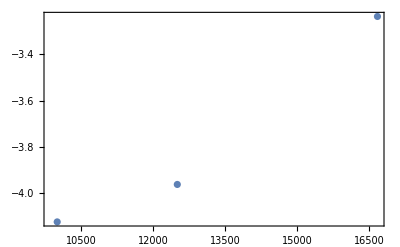

-5.56361+0.000137115 x

Part::partd: Part specification (-4.12274)⟦1⟧ is longer than depth of object.

General::munfl: 0.156322 2.97007693357×10^-1284 is too small to represent as a normalized machine number; precision may be lost.

Part::partd: Part specification (-4.12274)⟦2⟧ is longer than depth of object.

General::munfl: 0.156322 2.97007693357×10^-1284 is too small to represent as a normalized machine number; precision may be lost.

Part::partd: Part specification (-4.12274)⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

General::munfl: 0.156322 2.97007693357×10^-1284 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Part::partw: Part 4 of {{10000.,-4.12274},{12500.,-3.96121},{16666.7,-3.23653}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

0.000137115

{52718.2,5658.45}

```mathematica
etainverse=1/etaindex

logesctime=Log[(iterations*etaindex)]
simuldata=Table[{etainverse[[f]],logesctime[[f]]},{f,1,Length[etainverse]}];

(*ListLogLinearPlot[data]*)
lm=LinearModelFit[data,x,x];
Show[ListPlot[data],Plot[lm[x],{x,0,5}],Frame->True]
Normal[lm]
lossloss= loss[asaddleprecise,bsaddleprecise]/loss[areal,breal];
slope=lm["BestFitParameters"][[2]];


Eigenvalues[hesslossmin]
```

```mathematica
Eigenvalues[hesslossmin]
```

{51708.5,7594.75}

```mathematica
loss[1,1]
```

Part::partd: Part specification (-5.3817)⟦1⟧ is longer than depth of object.

General::munfl: Exp[-10000.] is too small to represent as a normalized machine number; precision may be lost.

Part::partd: Part specification (-5.3817)⟦2⟧ is longer than depth of object.

General::munfl: Exp[-10000.] is too small to represent as a normalized machine number; precision may be lost.

Part::partd: Part specification (-5.3817)⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

General::munfl: Exp[-10000.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Part::partw: Part 4 of {{10000.,-5.3817},{12500.,-3.85753},{16666.7,-2.98896}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

1
 |  |  |  |

```mathematica
iterations
```

{77,434,815}

## Correnti di probabilità

```mathematica
U[a_,b_]:= Log[loss[x,y]]/.{x->a,y->b};
T= 100;
Pstat[a_,b_]:=Exp[-U[x,y]/T]*(loss[x,y])^(-1)/.{x->a,y->b}; 
q=6;
Plot3D[Pstat[a,b],{a,-8,4},{b,0,7}, AxesLabel->{"a","b"},PlotRange->All]
```

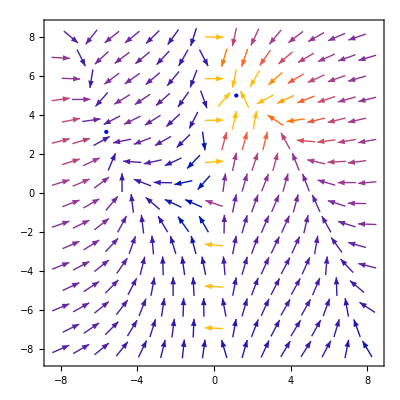

```mathematica
eta=0.00001;
partialx[a_,b_]:=-D[loss[x,y],x]*Pstat[x,y]-(eta)/(bsize)*(hesslossmin[[1]][[1]]*D[loss[x,y]*Pstat[x,y],x]+hesslossmin[[1]][[2]]*D[loss[x,y]*Pstat[x,y],y])/.{x->a,y->b};
partialy[a_,b_]:=-D[loss[x,y],y]*Pstat[x,y]-(eta/bsize)*(hesslossmin[[2]][[1]]*D[loss[x,y]*Pstat[x,y],x]+hesslossmin[[2]][[2]]*D[loss[x,y]*Pstat[x,y],y])/.{x->a,y->b};


J[a_,b_]:={partialx[x,y],partialy[x,y]} /.{x->a,y->b};
r=8;
vplot=VectorPlot[J[a,b],{a,-r,r}, {b,-r,r}];
g=Graphics[{PointSize[Large],Blue,Point[{areal,breal}]}];
locmin=Graphics[{PointSize[Large],Blue,Point[{arealmin,brealmin}]}];
locsad=Graphics[{PointSize[Large],Blue,Point[{asaddleprecise,bsaddleprecise}]}];
Show[vplot,g, locmin,locsad]
```

### Verifico la forma della distribuzione stazionaria

```mathematica
numeta=Table[i,{i,4,4}];
numpath=2;
bsize =10;
etasgd=0.00001;
(*simulo le traiettorie con la SDE con vari punti iniziali e guardo la distribuzione delle posizioni *)
timestep=etasgd;
maxtimes=1000;
bsizesgd =bsize;
vc= Table[{0,0},{i,1,numpath*maxtimes}];



(*calcolo l'hessiano, lo valuto su tutto il set e nel punto di minimo nello spazio dei parametri(che conosco)*)
hessloss[x_,y_,a_,b_]:= {{D[D[(y -fmod[x,a,b])^2,a],a],D[D[(y -fmod[x,a,b])^2,a],b]},{D[D[(y -fmod[x,a,b])^2,b],a],D[D[(y -fmod[x,a,b])^2,b],b]}};


(*vauluto l'hessiano nel minimo reale*)
hesslossmin= Sum[Sum[hessloss[data[[i,1]],data[[i,2]][[j]],x,y]/.{x->areal,y->breal},{j,1,ll}],{i,1,nn}];
sqrthesslossmin=MatrixPower[ hesslossmin, 1/2];

(*calcolo il gradiente su tutto il set di dati*)
gradlosstot[a_,b_]:=(1/ntot)*Sum[Sum[gradloss[data[[i,1]],data[[i,2]][[j]],x,y],{j,1,ll}],{i,1,nn}]/.{x->a,y->b}
w=8;
(*calcolo la dinamica*)
vc[[1]]={RandomReal[{-w,w}],RandomReal[{-w,w}]};

For[ite=2,ite≤numpath*maxtimes, ite++,
If[Mod[ite,maxtimes]==0,vc[[ite]]={RandomReal[{-w,w}],RandomReal[{-w,w}]}, 

Z={RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]};
Zscale= sqrthesslossmin.Z;
ai= vc[[ite-1]][[1]];
bi= vc[[ite-1]][[2]];
vc[[ite]][[1]]= ai-gradlosstot[x,y][[1]]*timestep+Sqrt[(2*etasgd/bsizesgd)*loss[x,y]]*Zscale[[1]]*Sqrt[timestep]/.{x->ai,y->bi};
vc[[ite]][[2]]= bi-gradlosstot[x,y][[2]]*timestep+Sqrt[(2*etasgd/bsizesgd)*loss[x,y]]*Zscale[[2]]*Sqrt[timestep]/.{x->ai,y->bi};
If[Mod[ite,100]==0, Print[ite, ", ", vc[[ite]]]];
];
]
```

100, {-4.43345,-0.148278}

200, {-4.8752,3.19039}

300, {-4.5024,0.936846}

400, {-4.57568,0.143126}

500, {-4.7672,1.31926}

600, {-5.24114,2.9757}

700, {-5.29963,1.18972}

800, {-5.92537,3.83018}

900, {-5.48093,3.84234}

1100, {3.25789,4.57587}

1200, {2.45906,4.31041}

1300, {2.08628,4.20948}

1400, {2.0892,4.77511}

1500, {2.04272,4.75589}

1600, {2.01908,4.62581}

1700, {2.06029,4.64182}

1800, {1.88629,4.92453}

1900, {1.77369,4.80955}

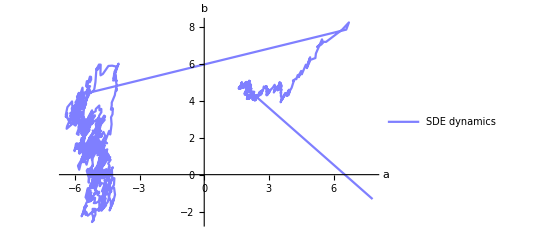

```mathematica
(*grafico sul piano le traiettorie*)
ListLinePlot[Table[{vc[[ite]][[1]],vc[[ite]][[2]]},{ite,1,Length[vc]}],PlotLegends->{"SDE dynamics"},PlotStyle->{Blue,Opacity[0.5]},
AxesLabel->{"a","b"},PlotRange->All]
```

```mathematica
(*Istogramma 3d dei dati*)
Histogram3D[vc]
```

-Graphics3D-

## Confronto i tre algoritmi

parametri stimati, SGD: {1.06375,4.95486}

parametri stimati, SDE: {1.33383,4.8979}

a0, b0: 0.0546396 0.178678

atrue, btrue: 1 5

areal, breal: 1.05877 4.95889

In-sample error, SGD: 3.07836

In-sample error, GD: 3.11127

In-sample error, SDE: 3.47031

Out-of-sample error, SGD: 3.70518

Out-of-sample error, GD: 3.84923

Out-of-sample error, SDE: 4.78779

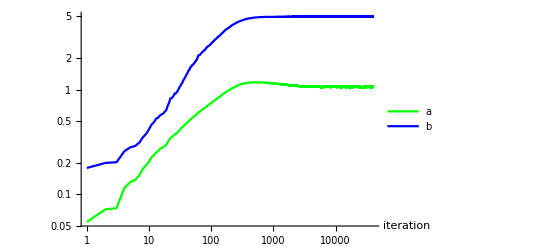

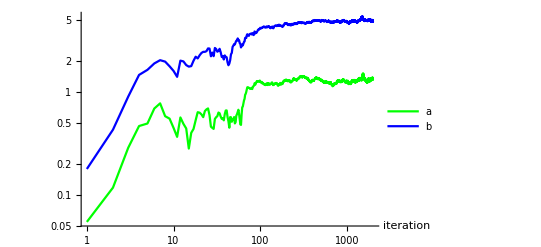

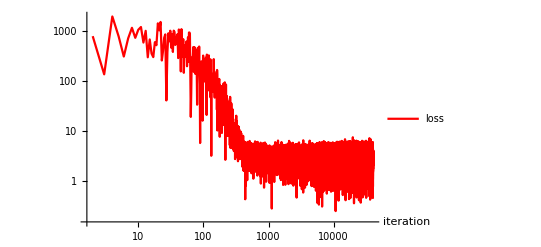

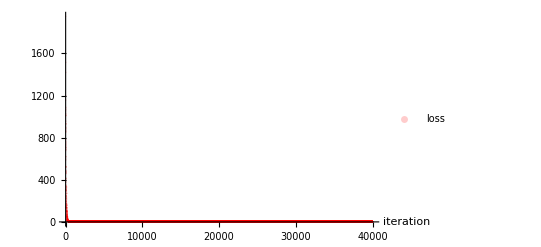

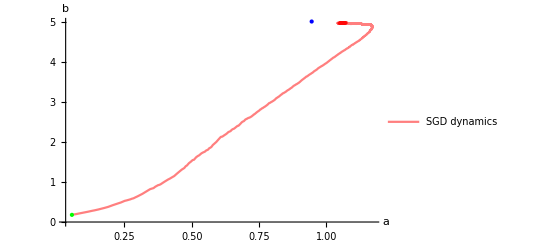

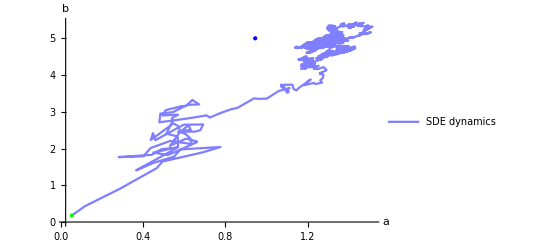

Part::partw: Part 1003 of {{0.0546396,0.178678},{0.0744683,0.204901},«8»,«992»} does not exist.

Part::partw: Part 1004 of {{0.0546396,0.178678},{0.0744683,0.204901},«8»,«992»} does not exist.

Part::partw: Part 1005 of {{0.0546396,0.178678},{0.0744683,0.204901},«8»,«992»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

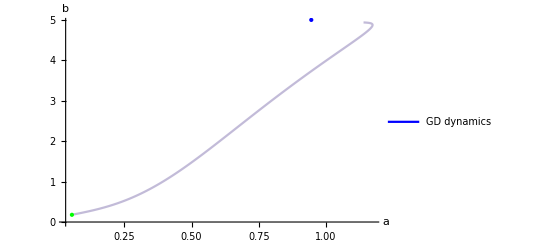

SystemDialogInput::nprmtv: SystemDialogInput is not currently supported within preemptive evaluations.

```mathematica
(* risultato: stima finale per a,b e confronto con quelli del modello vero *) 
Print["parametri stimati, SGD: ", v[[-1]]]
Print["parametri stimati, SDE: ", vc[[-1]]]
(*Print["parametri stimati, GD: ", vgd[[-1]]]*)
Print["a0, b0: ", a0," ",b0]
Print["atrue, btrue: ", atrue," ",btrue]
Print["areal, breal: ", areal," ",breal]
insamplesgd = loss[x,y]/.{x->v[[-1]][[1]],y->v[[-1]][[2]]};
insamplegd = loss[x,y]/.{x->vgd[[-1]][[1]],y->vgd[[-1]][[2]]};
insamplesde = loss[x,y]/.{x->vc[[-1]][[1]],y->vc[[-1]][[2]]};

outsamplesgd = lossp[x,y]/.{x->v[[-1]][[1]],y->v[[-1]][[2]]};
outsamplegd = lossp[x,y]/.{x->vgd[[-1]][[1]],y->vgd[[-1]][[2]]};
outsamplesde = lossp[x,y]/.{x->vc[[-1]][[1]],y->vc[[-1]][[2]]};

Print["In-sample error, SGD: ", insamplesgd," "]
Print["In-sample error, GD: ", insamplegd," "]
Print["In-sample error, SDE: ", insamplesde," "]

Print["Out-of-sample error, SGD: ", outsamplesgd," "]
Print["Out-of-sample error, GD: ", outsamplegd," "]
Print["Out-of-sample error, SDE: ", outsamplesde," "]

(* nei plot ricordati di mettere i nomi degli assi, le unità di misura se servono ecc. *)
Show[
ListLinePlot[Table[{ite,v[[ite]][[1]]},{ite,1,maxite}],
AxesOrigin->{0,0},
AxesLabel->{"iteration",""} ,ScalingFunctions->{"Log","Log"},PlotLegends->{"a"},PlotStyle->{Green}],
ListLinePlot[Table[{ite,v[[ite]][[2]]},{ite,1,maxite}],AxesOrigin->{0,0},ScalingFunctions->{"Log","Log"},
PlotLegends->{"b"},PlotStyle->{Blue}],PlotRange->All
]

Show[
ListLinePlot[Table[{ite,vc[[ite]][[1]]},{ite,1,maxtimes}],
AxesOrigin->{0,0},
AxesLabel->{"iteration",""} ,ScalingFunctions->{"Log","Log"},PlotLegends->{"a"},PlotStyle->{Green}],
ListLinePlot[Table[{ite,vc[[ite]][[2]]},{ite,1,maxtimes}],AxesOrigin->{0,0},
PlotLegends->{"b"},ScalingFunctions->{"Log","Log"},PlotStyle->{Blue}],PlotRange->All
]





ListLinePlot[Table[{ite,lossvalues[[ite]]},{ite,1,maxite}],PlotLegends->{"loss"},ScalingFunctions->{"Log","Log"},PlotStyle->{Red},
AxesLabel->{"iteration",""},PlotRange->All]

ListPlot[Table[{ite,lossvalues[[ite]]},{ite,1,maxite}],PlotLegends->{"loss"},PlotStyle->{Red,Opacity[0.2]},
AxesLabel->{"iteration",""},PlotRange->All]

initial=Graphics[{PointSize[Large],Green,Point[{a0,b0}]}]; (*punto di partenza*)
psgd=ListLinePlot[Table[{v[[ite]][[1]],v[[ite]][[2]]},{ite,1,maxite}],PlotLegends->{"SGD dynamics"},PlotStyle->{Red,Opacity[0.5]},
AxesLabel->{"a","b"},PlotRange->All];
Show[psgd,g,initial]

psde=ListLinePlot[Table[{vc[[ite]][[1]],vc[[ite]][[2]]},{ite,1,maxtimes}],PlotLegends->{"SDE dynamics"},PlotStyle->{Blue,Opacity[0.5]},
AxesLabel->{"a","b"},PlotRange->All];
Show[psde,g,initial]

pgd=ListLinePlot[Table[{vgd[[ite]][[1]],vgd[[ite]][[2]]},{ite,1,maxtimes}],PlotLegends->{"GD dynamics"},PlotStyle->{Blue,Opacity[0.5]},
AxesLabel->{"a","b"},PlotRange->All];
Show[pgd,g,initial]
```